```mathematica
SetDirectory[NotebookDirectory[]];
(files=FileNames["data/*.ods"])//TableForm
Needs["ErrorBarPlots`"]
```

data/erstemessung.ods
data/frequenzdoppel.ods
data/pockel.ods
data/zweitemesseung.ods

```mathematica
erste=First@Import[files[[1]]];
erste=erste[[1;;25]];
zweite=First@Import@files[[4]];
zweite=zweite[[1;;22]];
frequenz=First@Import@files[[2]];
frequenz=frequenz[[1;;24]];
pockels=First@Import@files[[3]];
pockels=pockels[[1;;21]];
```

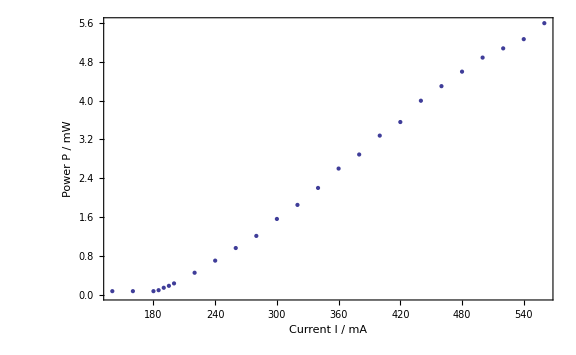

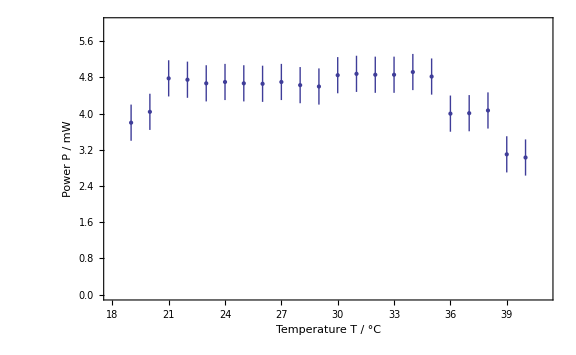

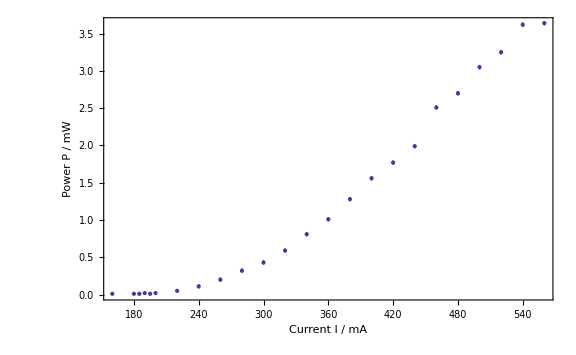

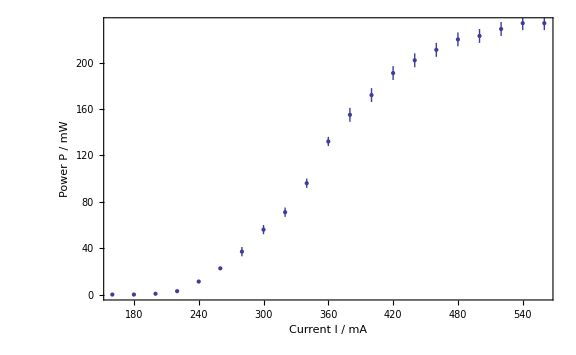

```mathematica
Show[ErrorListPlot[erste],ImageSize->Large,Frame->True,FrameLabel->{"Current I / mA","Power P / mW"},Axes->None]
Show[ErrorListPlot[zweite,PlotRange->{{18,41},{0,6}}],ImageSize->Large,Frame->True,FrameLabel->{"Temperature T / °C","Power P / mW"},Axes->None]
Show[ErrorListPlot[frequenz],ImageSize->Large,Frame->True,FrameLabel->{"Current I / mA","Power P / mW"},Axes->None]
Show[ErrorListPlot[pockels],ImageSize->Large,Frame->True,FrameLabel->{"Current I / mA","Power P / mW"},Axes->None]
```

```mathematica
(3362/4260) //N
```

0.789202

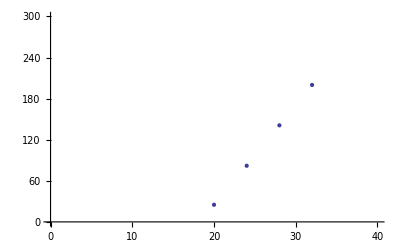

```mathematica
ListPlot[{{20,25},{32,200},{24,82},{28,141}},PlotRange->{{0,40},{0,300}}]
```

```mathematica
dat={{20,25},{32,200},{24,82},{28,141}};
```

```mathematica
NonlinearModelFit[dat,a*x+b,{a,b},x]
```

FittedModel[-267.6+14.6 x]

```mathematica
1/14.6
```

0.0684932